Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

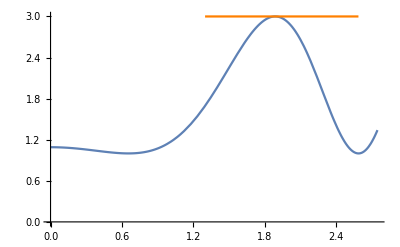

```mathematica
f[x_]:=2+Sin[x^2-2];
solns=Solve[f'[x]==0,x];
tangent=Max[f[x]/.solns];
p1 = Plot[2+Sin[x^2-2],{x,0,2.75},AxesOrigin->{0,0}];
p2=Plot[tangent,{x,1.9-0.6,1.9+0.69},PlotStyle->Orange];
fig=Show[p1,p2]
```

```mathematica
Export["~/school/FA22/PHYS163a/figs/minmax.png",fig]
```

~/school/FA22/PHYS163a/figs/minmax.png

```mathematica
solns//N
```

{{x→0.},{x→-0.655136},{x→0.655136},{x→-1.88966},{x→1.88966}}

```mathematica
√(2-π/2)//N
```

0.655136